```mathematica
Box2g[u_]:=Rectangle[{Min[First[u]],Min[Last[u]]},{Max[First[u]],Max[Last[u]]}];
Box2g[ix_,iy_,u_]:=Module[{value,min,max,mid},
value={u[[ix]],u[[iy]]};
min=Min/@value; max=Max/@value; mid=(Max[#]+Min[#])/2&/@value;
{Rectangle[min,max],PointSize[Large],Black,Point[mid]}
];

Pped2g[ix_,iy_, pped[x_,m_,u_]]:=Module[{x1,m1,u1},
x1={x[[ix]], x[[iy]]}; 
m1={{m[[ix,ix]], m[[ix,iy]]},{m[[iy,ix]], m[[iy,iy]]}};
u1={u[[ix]], u[[iy]]};
{GeometricTransformation[Rectangle[{Min[First[u1]],Min[Last[u1]]},{Max[First[u1]],Max[Last[u1]]}],AffineTransform[{m1,x1}]],
PointSize[Medium],Red,Point[x1]}
];

PpedD2g[ix_,iy_,pped2[x_,m_,u_, n_, v_]]:= Module[{x1,m1,u1,n1,v1},
x1={x[[ix]], x[[iy]]}; 
m1={{m[[ix,ix]], m[[ix,iy]]},{m[[iy,ix]], m[[iy,iy]]}};
u1={u[[ix]], u[[iy]]};
n1={{n[[ix,ix]], n[[ix,iy]]},{n[[iy,ix]], n[[iy,iy]]}};
v1={v[[ix]], v[[iy]]};
(*GeometricTransformation[Rectangle[{Min[First[u1]]+Min[First[v1]],Min[Last[u1]]+Min[Last[v1]]},{Max[First[u1]]+Max[First[v1]],Max[Last[u1]]+Max[Last[v1]]}],AffineTransform[{m1,x1}]]];*)
{GeometricTransformation[Rectangle[{Min[First[u1]],Min[Last[u1]]},{Max[First[u1]],Max[Last[u1]]}],AffineTransform[{m1,x1}]],
PointSize[Medium],Red,Point[x1]}];

(**)

pped2g[ix_,iy_,box[v_]]:=Module[{value,min,max,mid},
value={v[[ix]],v[[iy]]};
min=Min/@value; max=Max/@value; mid=(Max[#]+Min[#])/2&/@value;
{EdgeForm[{Thin,Black}],FaceForm[Opacity[0.1,LightGray]],Rectangle[min,max],PointSize[Small],Black,Point[mid]}
];
pped2g[ix_,iy_,pped[x_,m_,u_]]:=Module[{x1,m1,u1},
x1={x[[ix]], x[[iy]]}; 
m1={{m[[ix,ix]], m[[ix,iy]]},{m[[iy,ix]], m[[iy,iy]]}};
u1={u[[ix]], u[[iy]]};
{GeometricTransformation[Rectangle[{Min[First[u1]],Min[Last[u1]]},{Max[First[u1]],Max[Last[u1]]}],AffineTransform[{m1,x1}]],
PointSize[Medium],Red,Point[x1]}
];

pped2intv[iy_,box[v_]]:={Black,v[[iy]]};
pped2intv[iy_,pped[x_,m_,u_]]:=Module[{ix=1,x1,m1,u1},
x1={x[[ix]], x[[iy]]}; 
m1={{m[[ix,ix]], m[[ix,iy]]},{m[[iy,ix]], m[[iy,iy]]}};
u1={u[[ix]], u[[iy]]};
u1=m1.{Interval[{Min[First[u1]],Min[Last[u1]]}],Interval[{Max[First[u1]],Max[Last[u1]]}]}+x1;
{Red,u1[[2]][[1]]}
];

pipe2g[ix_,iy_,{t_,pped_}]:=Module[{res,value,min,max,mid},
If[ix>0,pped2g[ix,iy,pped],
res=pped2intv[iy,pped];
value={t,res[[2]]};
min=Min/@value; max=Max/@value; mid=(Max[#]+Min[#])/2&/@value;
{EdgeForm[{Thin,Black}],FaceForm[Opacity[0.1,LightGray]],Rectangle[min,max],PointSize[Large],res[[1]],Point[mid]}
]
];
```

```mathematica
pped2g[ix1_,ix2_,ix3_,box[v_]]:=Module[{value,min,max,mid},
value={v[[ix1]],v[[ix2]],v[[ix3]]};
min=Min/@value; max=Max/@value; mid=(Max[#]+Min[#])/2&/@value;
{(*EdgeForm[{Thin,Black}],FaceForm[Opacity[0.1,LightGray]],Cuboid[min,max],*)PointSize[Small],Black,Point[mid]}
];
pped2g[ix1_,ix2_,ix3_,pped[x_,m_,u_]]:=Module[{x1,m1,u1},
x1={x[[ix1]],x[[ix2]], x[[ix3]]}; 
m1={{m[[ix1,ix1]], m[[ix1,ix2]], m[[ix1,ix3]]},{m[[ix2,ix1]], m[[ix2,ix2]], m[[ix2,ix3]]},{m[[ix3,ix1]],m[[ix3,ix2]],m[[ix3,ix3]]}};
u1={u[[ix1]],u[[ix2]],u[[ix3]]};
{(*GeometricTransformation[Cuboid[{Min[First[u1]],Min[Last[u1]]},{Max[First[u1]],Max[Last[u1]]}],AffineTransform[{m1,x1}]],*)
PointSize[Medium],Red,Point[x1]}
];

pipe2g[ix1_,ix2_,ix3_,{t_,pped_}]:=Module[{res,value,min,max,mid},
If[ix1>0,pped2g[ix1,ix2,ix3,pped],
res=pped2intv[ix3,pped];
value={t,res[[2]]};
min=Min/@value; max=Max/@value; mid=(Max[#]+Min[#])/2&/@value;
{EdgeForm[{Thin,Black}],FaceForm[Opacity[0.1,LightGray]],Cuboid[min,max],PointSize[Large],res[[1]],Point[mid]}
(*Print[value];
Print[min];
Print[max]*)
]
];
```

```mathematica
Export["gg.eps",gg]
```

gg.eps

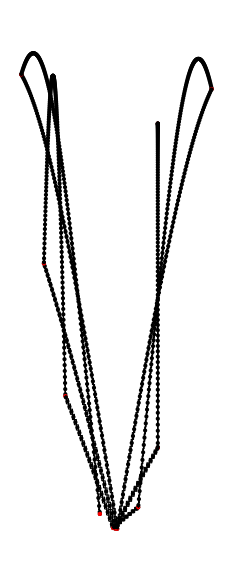

```mathematica
SetDirectory[NotebookDirectory[]];
list = <<"../src_ocaml/pped.dat";
list=list[[1;;-1]];
(*list1 = <<"../src_ocaml/pped1.dat";
list1=list1[[1;;-1]];
i=19;
Graphics[{Opacity[0.5],pped2g[1,2,list[[i]][[2]]],Red,pped2g[1,2,list1[[i]][[2]]](*,pped2g[1,2,list[[i+1]][[2]]],pped2g[1,2,list1[[i+1]][[2]]]*)}]*)
g=Graphics[pipe2g[1,3,#]& /@ list]
```

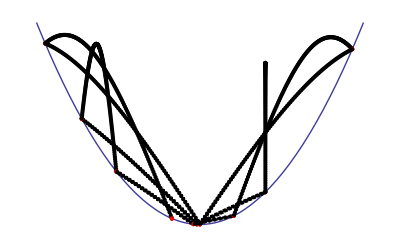

```mathematica
gg=Show[{Plot[2x^2,{x,-2.5,2.5},Axes->None],g}]
```

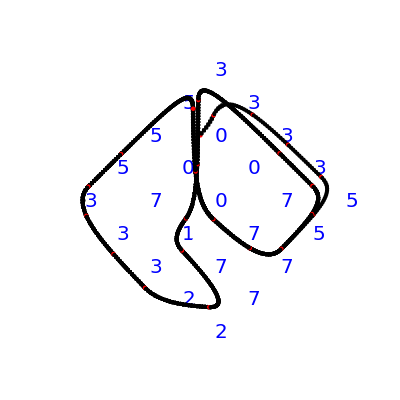

```mathematica
wind={{4,6,6,6,4},{4,0,1,1,4},{4,2,1,1,4},{3,0,0,0,4},{3,0,0,6,6}};
rs={};Do[Do[rs=Join[rs,{White,Rotate[Rectangle[(2/Sqrt[2]){5-i,5-j},(2/Sqrt[2]){6-i,6-j}],Pi/4,{0,0}],Blue,Text[Style[Mod[wind[[j]][[6-i]]+7,8],FontSize->20],RotationTransform[Pi/4][(2/Sqrt[2]){5.8-i,5.15-j}]]}],{j,5}],{i,5}];
gg=Show[{Graphics[Join[{EdgeForm[Thin],White},rs]],g}]
```

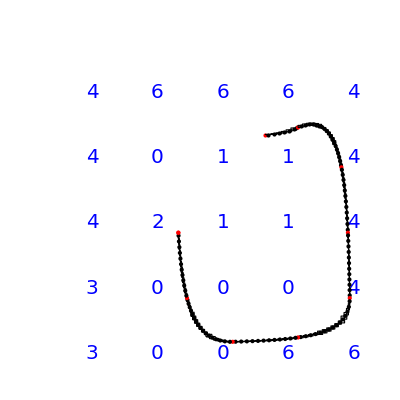

```mathematica
wind={{4,6,6,6,4},{4,0,1,1,4},{4,2,1,1,4},{3,0,0,0,4},{3,0,0,6,6}};
rs={};Do[Do[rs=Join[rs,{White,Rectangle[{5-i,5-j},{6-i,6-j}],Blue,Text[Style[wind[[j]][[6-i]],FontSize->20],{5.85-i,5.15-j}]}],{j,5}],{i,5}];g=Show[{Graphics[Join[{EdgeForm[Thin],White},rs]],g}]
```

```mathematica
list = <<"../src_ocaml/pped.dat";
n=4;
g=Graphics3D[pipe2g[1,2,3,#]& /@ list];
g1=Graphics3D[pipe2g[1,2,n,#]& /@ list];
g2=Graphics3D[pipe2g[n,2,3,#]& /@ list];
g3=Graphics3D[pipe2g[1,n,3,#]& /@ list];
Show[{g,g1,g2,g3}]
```

-Graphics3D-

```mathematica
list = <<"bb-parabola-4d.dat";
g=Graphics3D[pipe2g[1,2,3,#]& /@ list];
g1=Graphics3D[pipe2g[1,2,4,#]& /@ list];
g2=Graphics3D[pipe2g[4,2,3,#]& /@ list];
g3=Graphics3D[pipe2g[1,4,3,#]& /@ list];
Show[{g,g1,g2,g3}]
```

-Graphics3D-

```mathematica
SetDirectory[NotebookDirectory[]];
list = <<pendulum.dat;
Graphics[pipe2g[0,1,#]& /@ list]
```

-Graphics-